```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Read the data file and reshape it *)
```

```mathematica
ncol=5;c=12.635047045;
data=ReadList["bs_mat.out",Number];
data=data/.$Failed->0;
nline=Length[data]/ncol;
datashaped=ArrayReshape[data,{nline,ncol}]
```

```mathematica
(* Check the values of the grid bounds *)
```

```mathematica
xmin=Min[datashaped[[All,1]]]
xmax=Max[datashaped[[All,1]]]
θmin=Min[datashaped[[All,2]]]
θmax=Max[datashaped[[All,2]]]
```

1/1000000

1

0

1.5708

```mathematica
(* Useful things for later *)
```

```mathematica
gridx=DeleteDuplicates[datashaped[[All,1]]];
R[x_]:=c x/(1-x);
```

```mathematica
(* Construct tabulated values of the scalar field in compactified coordinates and interpolate *)
```

```mathematica
dataϕ=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,3]]},{i,nline}];
```

```mathematica
(* ϕ: scalar field profile in compactified coordinates 
ϕρz: scalar field profile in cylindrical coordinates *)
```

```mathematica
ϕ=Interpolation[dataϕ,InterpolationOrder->3]
ϕρz[ρ_,z_]:=ϕ[Sqrt[ρ^2+z^2]/(Sqrt[ρ^2+z^2]+c),ArcTan[z,ρ]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[ϕ[x,θ],{x,xmin,xmax},{θ,θmin,θmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
ρmax=80;zmax=ρmax;
Plot3D[ϕρz[ρ,z]^2,{ρ,0,ρmax},{z,0,zmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
(* Compute the distance (meaningful for dipolar stars only) *)
```

```mathematica
FindMaximum[{ϕ[x,θmin],0<=x<=1},{x,0.4}]
c x/(1-x)/.%[[2]]
%*2.0
```

{0.00821048,{x→0.650875}}

23.5556

47.1112

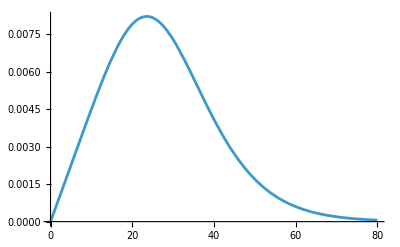

```mathematica
Plot[ϕρz[θmin,z],{z,0,80},PlotRange->All]
```

```mathematica
(* Construct tabulated values of dx(f) (derivative of Subscript[g, 00]) in compactified coordinates *)
```

```mathematica
datadxf=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,5]]},{i,nline}];
```

```mathematica
(* Compute the mass : first extract the values at infinity and then compute the mean *)
```

```mathematica
dxfinf=Cases[datadxf,{{xmax,y_},f_}:>f];
Minf=Mean[dxfinf]/G
```

72.0243

```mathematica
(* Construct tabulated values of dM(x) (integrand of the komar mass) in compactified coordinates *)
```

```mathematica
datadM=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,6]]},{i,nline}];
```

```mathematica
(* Take only the values at θ=1e-6 (meaningful for spherical stars only) and interpolate *)
```

```mathematica
dMr=Cases[datadM,{{x_,θmin},f_}:>{x,f}];
dM=Interpolation[dMr,InterpolationOrder->3]
```

InterpolatingFunction[…]

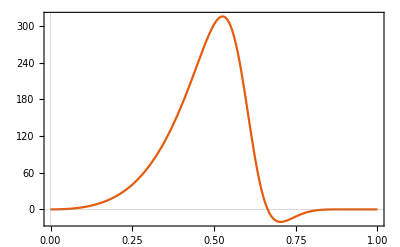

```mathematica
Plot[dM[x],{x,xmin,1},PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
(* Compute the integrated values of dM and interpolate *)
```

```mathematica
Mint=Table[{gridx[[i]],NIntegrate[dM[x],{x,xmin,gridx[[i]]}]},{i,Length[gridx]}];
M=Interpolation[Mint,InterpolationOrder->3]
```

InterpolatingFunction[…]

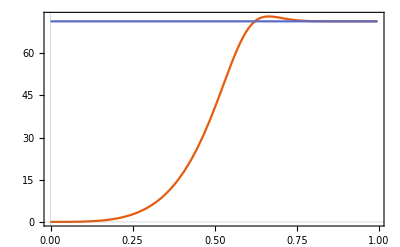

71.3055

```mathematica
Plot[{M[x],M[xmax]},{x,xmin,xmax},PlotRange->All,PlotTheme->"Scientific"]
M[xmax]
```

```mathematica
(* Compute the 99% radius *)
```

```mathematica
x99=0.6;
FindRoot[M[x]-0.99*Minf,{x,x99,xmin,xmax},Method->"AffineCovariantNewton",AccuracyGoal->Infinity]
c x/(1-x)/.%
```

{x→0.621741}

1.64369

```mathematica
(* Re-scaled profile (meaningfull for spherical stars only) *)
```

```mathematica
μ=1;ω=0.439161;
k=Sqrt[μ^2-ω^2];
```

```mathematica
Exp[k*0.7133]
```

1.89806

```mathematica
dataϕt=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,7]]},{i,nline}];
dataϕt2d=Cases[dataϕt,{{x_,θmin},f_}:>{x,f}];
dataϕ2d=Cases[dataϕ,{{x_,θmin},f_}:>{x,f}];
ϕ2d=Interpolation[dataϕ2d,InterpolationOrder->3]
ϕt2d=Interpolation[dataϕt2d,InterpolationOrder->3]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

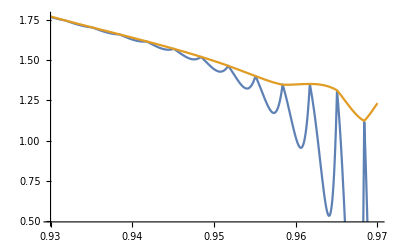

```mathematica
Plot[{ϕ2d[x]R[x]Exp[k R[x]],ϕt2d[x]},{x,0.93,0.97}]
```

```mathematica
R[0.96]
ϕt2d[0.96]
```

24.

1.34865

```mathematica
(* Construct tabluated values of the energy density in compactified coordinates and interpolate *)
```

```mathematica
dataTtt=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,4]]},{i,nline}];
```

```mathematica
Ttt=Interpolation[dataTtt,InterpolationOrder->3]
Tttρz[ρ_,z_]:=Ttt[Sqrt[ρ^2+z^2]/(Sqrt[ρ^2+z^2]+c),ArcTan[z,ρ]]
Tttxyz[x_,y_,z_]:=Tttρz[Sqrt[x^2+y^2],z]
```

-6             -6
InterpolatingFunction[{{1. 10  , 1.}, {1. 10  , 3.14159}}, <>]

```mathematica
Plot3D[Ttt[x,θ],{x,xmin,xmax},{θ,θmin,θmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
Plot3D[Tttρz[ρ,z],{ρ,0,ρmax},{z,-zmax,zmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

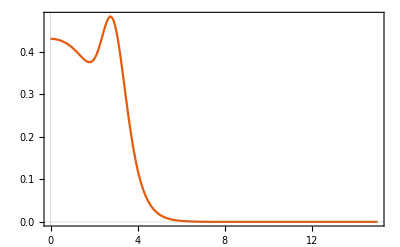

```mathematica
Plot[Tttρz[1,z],{z,0,zmax},PlotRange->All,PlotTheme->"Scientific"]
```

```mathematica
(* Compute the distance (meaningful for dipolar stars only) *)
```

```mathematica
FindMaximum[{Ttt[x,θmin],0<=x<=1},{x,0.4}]
c x/(1-x)/.%[[2]]
%*2.0
```

{0.62225,{x→0.882355}}

7.50016

15.0003

```mathematica
(* 3D plot of isosurfaces *)
```

{0.1,0.025,0.00625}

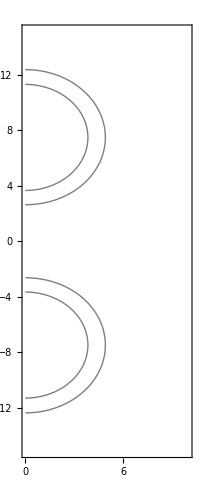

```mathematica
val={0.1,0.025,0.00625}
ContourPlot[Tttρz[ρ,z],{ρ,0,ρmax},{z,-zmax,zmax},Contours->val,ContourShading->False,AspectRatio->Automatic,PlotPoints->100]
```

```mathematica
ContourPlot3D[Tttxyz[x,y,z],{x,-ρmax,ρmax},{y,0,ρmax},{z,-zmax,zmax},Contours->val,ContourStyle->Directive[LightBlue,Specularity[White,300]],Boxed->False,Mesh->None,BoxRatios->Automatic,Axes->False]
```

-Graphics3D-